## Brian — PS 11 — 2025-03-18 — Solution

## EIWL3 Sections 29 and 30

## !! HELP — I HAD TROUBLE WITH 30.7 and 30.10 !!

## Exercises from EIWL3 Section 29

```mathematica
(* 29.1 *) Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
(* 29.2 *) Array[Prime[#]-Prime[#-1]&,99,2]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

```mathematica
(* 29.3*) Array[Plus,{10,10}]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
(* 29.4 *) FoldList[Times,Range[10]]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
(* 29.5 *) FoldList[Times,Array[Prime,10]]
```

{2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

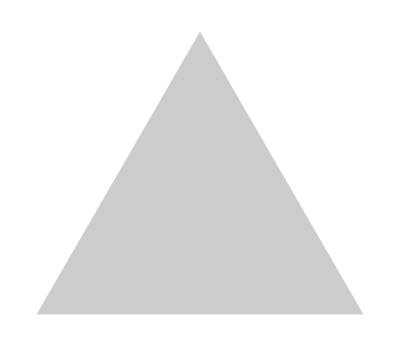
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 29.6 *) FoldList[ImageAdd,Graphics/@Array[{Opacity[0.2],RegularPolygon[#]}&,6,3]]
```

## Exercises from EIWL3 Section 30

```mathematica
(* 30.1 *) Thread[Alphabet[]->LetterNumber/@Alphabet[]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
(* 30.2 *) Partition[Alphabet[],6]//Grid
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

```mathematica
(* 30.3 *) Partition[IntegerDigits[2^1000],50]//Grid[#,Frame->All]&
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

```mathematica
(* 30.4 *) Partition[Characters[StringTake[WikipediaData["computers"],400]],20]//Grid[#,Frame->All]&
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | m | a | c | h
i | n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g
r | a | m | m | e | d |   | t | o |   | a | u | t | o | m | a | t | i | c | a
l | l | y |   | c | a | r | r | y |   | o | u | t |   | s | e | q | u | e | n
c | e | s |   | o | f |   | a | r | i | t | h | m | e | t | i | c |   | o | r
  | l | o | g | i | c | a | l |   | o | p | e | r | a | t | i | o | n | s |  
( | c | o | m | p | u | t | a | t | i | o | n | ) | . |   | M | o | d | e | r
n |   | d | i | g | i | t | a | l |   | e | l | e | c | t | r | o | n | i | c
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | T | h | e |   | t
e | r | m |   | c | o | m | p | u | t | e | r |   | s | y | s | t | e | m |  
m | a | y |   | r | e | f | e | r |   | t | o |   | a |   | n | o | m | i | n
a | l | l | y |   | c | o | m | p | l | e | t | e |   | c | o | m | p | u | t
e | r |   | t | h | a | t |   | i | n | c | l | u | d | e | s |   | t | h | e
  | h | a | r | d | w | a | r | e | , |   | o | p | e | r | a | t | i | n | g

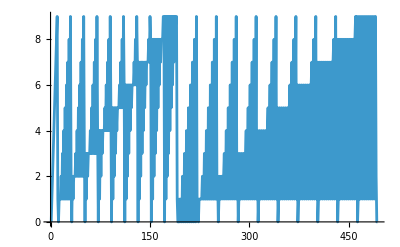

```mathematica
(* 30.5 *)ListLinePlot[Flatten[ IntegerDigits/@Range[0,200]]]
```


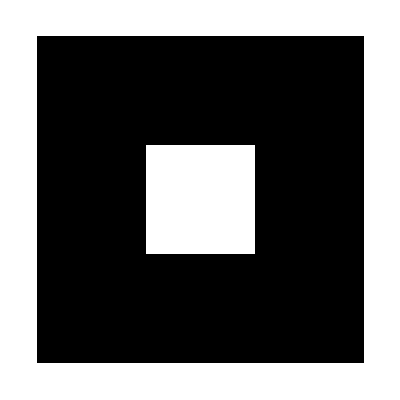
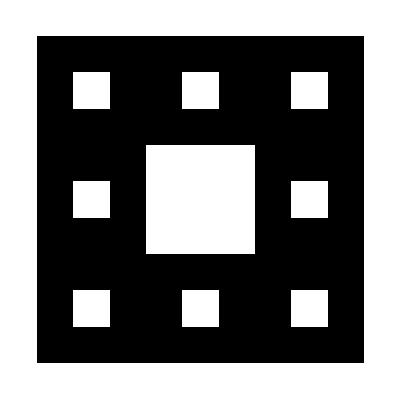
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 30.6 *) ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]
```

```mathematica
(* 30.7 *) myList=Array[{#1, #2, Sqrt[#1^2+#2^2]}&,{5,5}]
```

{{{1,1,√2},{1,2,√5},{1,3,√10},{1,4,√17},{1,5,√26}},{{2,1,√5},{2,2,2 √2},{2,3,√13},{2,4,2 √5},{2,5,√29}},{{3,1,√10},{3,2,√13},{3,3,3 √2},{3,4,5},{3,5,√34}},{{4,1,√17},{4,2,2 √5},{4,3,5},{4,4,4 √2},{4,5,√41}},{{5,1,√26},{5,2,√29},{5,3,√34},{5,4,√41},{5,5,5 √2}}}

```mathematica
Select[myList,IntegerQ[Last[#]]&]
```

{}

```mathematica
(* 30.8 *) Array[Length[Last[Sort[Split[IntegerDigits[2^#]]]]]&,100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
(* 30.9 *) Gather[Array[IntegerName,100],First[Characters[#1]]==First[Characters[#2]]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
(* 30.10 *) Sort[Take[WordList[],50],Last[Characters[#1]]<Last[Characters[#2]]&]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abeam,abed,aberrant,aberration,abet,abettor,abeyance,abhor,abhorrence,abhorrent,abidance,abide,abiding,ability,abject,abjection,abjectly}

```mathematica
(* 30.11 *) Sort[Array[#^2&,20],First[IntegerDigits[#1]]<First[IntegerDigits[#2]]&]
```

{196,169,144,121,100,16,1,289,256,225,25,361,324,36,400,49,4,64,81,9}

```mathematica
(* 30.12 *) Sort[Array[IntegerName,20],StringLength[#1]<StringLength[#2]&]
```

{ten,six,two,one,nine,five,four,eight,seven,three,twenty,twelve,eleven,sixteen,fifteen,nineteen,eighteen,fourteen,thirteen,seventeen}

```mathematica
(* 30.13 *) Gather[RandomChoice[WordList[],20],StringLength[#1]==StringLength[#2]&]
```

{{shine},{swelled,stumble,descant},{assemble,methanol,loveless,strainer},{niggle,gossip,untidy,carpel},{eyeglasses,underskirt},{opalescence,propinquity},{vent},{simultaneity},{UFO},{corollary}}

```mathematica
(* 30.14 *) Complement[Alphabet["Russian"],Alphabet["Ukrainian"]]
```

{ъ,ы,э,ё}

```mathematica
(* 30.15 *) Intersection[Array[#^2&,100],Array[#^3&,100]]
```

{1,64,729,4096}

```mathematica
(* 30.16 *) Intersection[EntityList[EntityClass["Country","GroupOf8"]],EntityList[EntityClass["Country","NATO"]]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
(* 30.17 *) Transpose[Permutations[Range[4]]]//Grid
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
(* 30.18 *) Permutations[Characters["hello"]]
```

{{h,e,l,l,o},{h,e,l,o,l},{h,e,o,l,l},{h,l,e,l,o},{h,l,e,o,l},{h,l,l,e,o},{h,l,l,o,e},{h,l,o,e,l},{h,l,o,l,e},{h,o,e,l,l},{h,o,l,e,l},{h,o,l,l,e},{e,h,l,l,o},{e,h,l,o,l},{e,h,o,l,l},{e,l,h,l,o},{e,l,h,o,l},{e,l,l,h,o},{e,l,l,o,h},{e,l,o,h,l},{e,l,o,l,h},{e,o,h,l,l},{e,o,l,h,l},{e,o,l,l,h},{l,h,e,l,o},{l,h,e,o,l},{l,h,l,e,o},{l,h,l,o,e},{l,h,o,e,l},{l,h,o,l,e},{l,e,h,l,o},{l,e,h,o,l},{l,e,l,h,o},{l,e,l,o,h},{l,e,o,h,l},{l,e,o,l,h},{l,l,h,e,o},{l,l,h,o,e},{l,l,e,h,o},{l,l,e,o,h},{l,l,o,h,e},{l,l,o,e,h},{l,o,h,e,l},{l,o,h,l,e},{l,o,e,h,l},{l,o,e,l,h},{l,o,l,h,e},{l,o,l,e,h},{o,h,e,l,l},{o,h,l,e,l},{o,h,l,l,e},{o,e,h,l,l},{o,e,l,h,l},{o,e,l,l,h},{o,l,h,e,l},{o,l,h,l,e},{o,l,e,h,l},{o,l,e,l,h},{o,l,l,h,e},{o,l,l,e,h}}

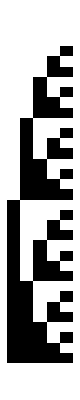

```mathematica
(* 30.19 *)ArrayPlot[Tuples[{0,1},5]]
```

```mathematica
(* 30.20 *) Table[RandomChoice[Alphabet[],5],5]
```

{{q,z,r,m,s},{e,p,e,y,r},{t,t,e,t,f},{a,t,x,q,c},{b,b,g,s,z}}

```mathematica
(* 30.21 *) Flatten[Array[{#1, #2, #3}&,{2,2,2}],2]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}